```mathematica
(* JSQ system time distribution solver *)
(* FIFO service, homogeneous system *)
(* buffer size *)
B=5; 
(* arrival rate *)
λ=5/4; 
(* service rate curve *)
μ={1,11/10,12/10,13/10,14/10}; 
i0=4; 
(* stationary distribution (from differential equation solution) *)
{ν[0],ν[1],ν[2],ν[3],ν[4],ν[5]}={0,0,0,1/2,1/2,0}; 
(* upkeep *)
z0=ν[i0-1]μ[[i0-1]];
(* equations for the Laplace transforms *)
eqns={};
For[j=1,j≤i0,j++,
For[i=1,i≤j,i++,
eqn={};
If[(j<i0-1),
eqn={Hs[i,j]==Hs[i,j+1]}];
If[(i==1)&&(j==i0-1),
eqn={Hs[1,i0-1]==
((λ-z0)/ν[i0-1]+μ[[i0-1]])/(s+(λ-z0)/ν[i0-1]+μ[[i0-1]])*
(μ[[i0-1]]/((λ-z0)/ν[i0-1]+μ[[i0-1]])+((λ-z0)/ν[i0-1])/((λ-z0)/ν[i0-1]+μ[[i0-1]])Hs[1,i0])}];
If[(i>1)&&(j==i0-1),
eqn={Hs[i,i0-1]==
((λ-z0)/ν[i0-1]+μ[[i0-1]])/(s+(λ-z0)/ν[i0-1]+μ[[i0-1]])*
(((λ-z0)/ν[i0-1])/((λ-z0)/ν[i0-1]+μ[[i0-1]])Hs[i,i0]+μ[[i0-1]]/((λ-z0)/ν[i0-1]+μ[[i0-1]])*Hs[i-1,i0-2])}];
If[(i==1)&&(j>i0-1),
eqn={Hs[1,j]==
μ[[j]]/(s+μ[[j]])}];
If[(i>1)&&(j>i0-1),
eqn={Hs[i,j]==
μ[[j]]/(s+μ[[j]])*Hs[i-1,j-1]}];
eqns = eqns ~Join~eqn;
];
];
```

```mathematica
(* solution of the equations for the Laplace transform *)
{Hs3,Hs4}={Hs[3,3],Hs[4,4]}/.Solve[eqns][[1]];
Hssol=μ[[3]]ν[3]/λ*Hs3+μ[[4]]ν[4]/λ*Hs4;
Hsfun[s_]:=Evaluate[Hssol];
```

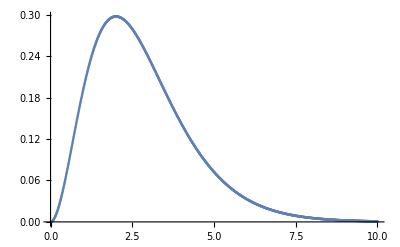

L:\Kut2\MM\hist_jsq.csv

```mathematica
(* inverse Laplace transform, uses ILT package *)Ht=ILT[Hsfun,Table[t,{t,1/100,10,1/100}],60,"cme",100];
Htlist = Table[{i/100,Ht[[i]]},{i,1,1000}];
ListPlot[Htlist]
Export["L:\\Kut2\\MM\\hist_jsq_B5.csv",N[Htlist,6],"Table","FieldSeparator"->","]
```

```mathematica
(* random system time distribution solver *)
(* FIFO service, homogeneous system *)
B=5;
λ=5/4;
μ={1,11/10,12/10,13/10,14/10};
c=1/Sum[∏_(j=1)^i λ/μ[[j]],{i,0,B}];
{ν[0],ν[1],ν[2],ν[3],ν[4],ν[5]}=c*Table[∏_(j=1)^i λ/μ[[j]],{i,0,B}];eqns={};
For[j=1,j≤B,j++,
For[i=1,i≤j,i++,
eqn={};
If[(i>1&&j≤B-1),
eqn={Hs[i,j]==
(λ+μ[[j]])/(s+λ+μ[[j]])*
(λ/(λ+μ[[j]])Hs[i,j+1]+μ[[j]]/(λ+μ[[j]])Hs[i-1,j-1])}];
If[(i>1)&&(j==B),
eqn={Hs[i,B]==
μ[[B]]/(s+μ[[B]])*Hs[i-1,B-1]}];
If[(i==1)&&(j≤B-1),
eqn={Hs[1,j]==(λ+μ[[j]])/(s+λ+μ[[j]])*(λ/(λ+μ[[j]])*Hs[i,j+1]+
μ[[j]]/(λ+μ[[j]]))}];
If[(i==1)&&(j==B),
eqn={Hs[1,B]==
μ[[B]]/(s+μ[[B]])}];
eqns = eqns ~Join~eqn;
];
];
```

```mathematica
{Hs1,Hs2,Hs3,Hs4,Hs5}={Hs[1,1],Hs[2,2],Hs[3,3],Hs[4,4],Hs[5,5]}/.Solve[eqns][[1]];
Hssol=ν[0]*Hs1+ν[1]*Hs2+ν[2]*Hs3+ν[3]*Hs4+ν[4]*Hs5;
Hsfun[s_]:=Evaluate[Hssol];
(* due to data loss, normalization constant necessary *)
norm=1-ν[B];
```

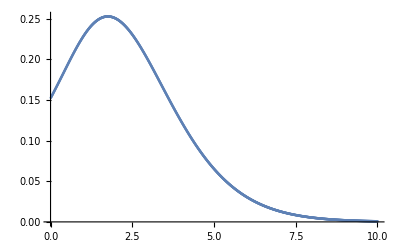

0.998869635356750394219299414340237846719181083717182537939831189348129580443932001

L:\Kut2\MM\hist_random_B5.csv

```mathematica
Ht=ILT[Hsfun,Table[t,{t,1/100,10,1/100}],60,"cme",100];
Htlist = Table[{i/100,Ht[[i]]/norm},{i,1,1000}];
ListPlot[Htlist]
Export["L:\\Kut2\\MM\\hist_random_B5.csv",N[Htlist,6],"Table","FieldSeparator"->","]
```

```mathematica
(* JIQ system time distribution solver *)
(* FIFO service, homogeneous system *)
B=5;
λ=5/4;
μ={1,11/10,12/10,13/10,14/10};
{ν[0],ν[1],ν[2],ν[3],ν[4],ν[5]}={0, 29129,25387,20283,14958,10243}/100000;
z0=ν[1]μ[[1]];
eqns={};
For[j=1,j≤B,j++,
For[i=1,i≤j,i++,
eqn={};
If[(i==1)&&(j==B),
eqn={Hs[1,B]==μ[[B]]/(s+μ[[B]])}];
If[(i>1)&&(j==B),
eqn={Hs[i,B]==μ[[B]]/(s+μ[[B]])Hs[i-1,B-1]}];
If[(i==1)&&(j≤B-1),
eqn={Hs[1,j]==
((λ-z0)+μ[[j]])/(s+(λ-z0)+μ[[j]])((λ-z0)/((λ-z0)+μ[[j]])Hs[1,j+1]+μ[[j]]/((λ-z0)+μ[[j]]))}];
If[(i>1)&&(j≤B-1),
eqn={Hs[i,j]==((λ-z0)+μ[[j]])/(s+(λ-z0)+μ[[j]])*((λ-z0)/((λ-z0)+μ[[j]])*Hs[i,j+1]+μ[[j]]/((λ-z0)+μ[[j]])*Hs[i-1,j-1])}];
eqns = eqns ~Join~eqn;
];
];
```

```mathematica
{Hs1,Hs2,Hs3,Hs4,Hs5}={Hs[1,1],Hs[2,2],Hs[3,3],Hs[4,4],Hs[5,5]}/.Solve[eqns][[1]];
Hssol=(μ[[1]]ν[1])/λ*Hs1+(1-(μ[[1]]ν[1])/λ)*(ν[1]*Hs2+ν[2]*Hs3+ν[3]*Hs4+ν[4]*Hs5);
Hsfun[s_]:=Evaluate[Hssol];
norm = 1-ν[B]*(λ-z0)/λ;
```

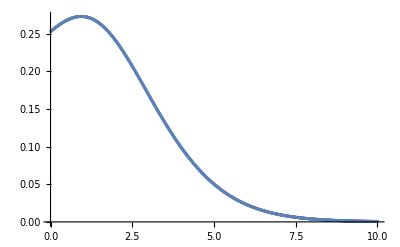

L:\Kut2\MM\hist_jiq.csv

```mathematica
Ht=ILT[Hsfun,Table[t,{t,1/100,10,1/100}],60,"cme",100];
(Htlist = Table[{i/100,Ht[[i]]/norm},{i,1,1000}];)
ListPlot[Htlist]
Export["L:\\Kut2\\MM\\hist_jiq_B5.csv",N[Htlist,6],"Table","FieldSeparator"->","]
```

```mathematica
(* JSQ(2) system time distribution solver *)
(* FIFO service, homogeneous system *)
B=5;
d=2;
λ=5/4;
μ={1,11/10,12/10,13/10,14/10};
{ν[0],ν[1],ν[2],ν[3],ν[4],ν[5]}={028364,069902,148803,256467,308090,188374}/1000000;
z[5]=ν[5];
z[4]=ν[4]+ν[5];
z[3]=ν[3]+ν[4]+ν[5];
z[2]=ν[2]+ν[3]+ν[4]+ν[5];
z[1]=ν[1]+ν[2]+ν[3]+ν[4]+ν[5];
z[0]=1;
fpν[0]=(z[0]^d-z[1]^d)/ν[0];
fpν[1]=(z[1]^d-z[2]^d)/ν[1];
fpν[2]=(z[2]^d-z[3]^d)/ν[2];
fpν[3]=(z[3]^d-z[4]^d)/ν[3];
fpν[4]=(z[4]^d-z[5]^d)/ν[4];
eqns={};
For[j=1,j≤B,j++,
For[i=1,i≤j,i++,
eqn={};
If[(i>1&&j≤B-1),
eqn={Hs[i,j]==
(λ fpν[i]+μ[[j]])/(s+λ fpν[i]+μ[[j]])*
((λ fpν[i])/(λ fpν[i]+μ[[j]])Hs[i,j+1]+μ[[j]]/(λ fpν[i]+μ[[j]])Hs[i-1,j-1])}];
If[(i>1)&&(j==B),
eqn={Hs[i,B]==
μ[[B]]/(s+μ[[B]])*Hs[i-1,B-1]}];
If[(i==1)&&(j≤B-1),
eqn={Hs[1,j]==(λ fpν[i]+μ[[j]])/(s+λ fpν[i]+μ[[j]])*((λ fpν[i])/(λ fpν[i]+μ[[j]])*Hs[i,j+1]+
μ[[j]]/(λ fpν[i]+μ[[j]]))}];
If[(i==1)&&(j==B),
eqn={Hs[1,B]==
μ[[B]]/(s+μ[[B]])}];
eqns = eqns ~Join~eqn;
];
];
```

```mathematica
{Hs1,Hs2,Hs3,Hs4,Hs5}={Hs[1,1],Hs[2,2],Hs[3,3],Hs[4,4],Hs[5,5]}/.Solve[eqns][[1]];
Hssol=(z[0]^d-z[1]^d)*Hs1+(z[1]^d-z[2]^d)*Hs2+(z[2]^d-z[3]^d)*Hs3+(z[3]^d-z[4]^d)*Hs4+(z[4]^d-z[5]^d)*Hs5;
Hsfun[s_]:=Evaluate[Hssol];
(* due to data loss, normalization constant necessary *)
norm=1-z[B]^d;
```

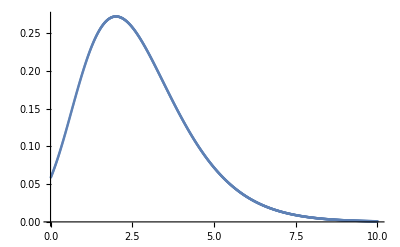

L:\Kut2\MM\hist_jsq2_B5.csv

```mathematica
Ht=ILT[Hsfun,Table[t,{t,1/100,10,1/100}],60,"cme",200];
Htlist = Table[{i/100,Ht[[i]]/norm},{i,1,1000}];
ListPlot[Htlist]
Export["L:\\Kut2\\MM\\hist_jsq2_B5.csv",N[Htlist,6],"Table","FieldSeparator"->","]
```

```mathematica
(* JSQ(5) system time distribution solver *)
(* FIFO service, homogeneous system *)
B=5;
d=5;
λ=5/4;
μ={1,11/10,12/10,13/10,14/10};
{ν[0],ν[1],ν[2],ν[3],ν[4],ν[5]}={002473,015364,083704,341634,509757,047068}/1000000;
z[5]=ν[5];
z[4]=ν[4]+ν[5];
z[3]=ν[3]+ν[4]+ν[5];
z[2]=ν[2]+ν[3]+ν[4]+ν[5];
z[1]=ν[1]+ν[2]+ν[3]+ν[4]+ν[5];
z[0]=1;
fpν[0]=(z[0]^d-z[1]^d)/ν[0];
fpν[1]=(z[1]^d-z[2]^d)/ν[1];
fpν[2]=(z[2]^d-z[3]^d)/ν[2];
fpν[3]=(z[3]^d-z[4]^d)/ν[3];
fpν[4]=(z[4]^d-z[5]^d)/ν[4];
eqns={};
For[j=1,j≤B,j++,
For[i=1,i≤j,i++,
eqn={};
If[(i>1&&j≤B-1),
eqn={Hs[i,j]==
(λ fpν[i]+μ[[j]])/(s+λ fpν[i]+μ[[j]])*
((λ fpν[i])/(λ fpν[i]+μ[[j]])Hs[i,j+1]+μ[[j]]/(λ fpν[i]+μ[[j]])Hs[i-1,j-1])}];
If[(i>1)&&(j==B),
eqn={Hs[i,B]==
μ[[B]]/(s+μ[[B]])*Hs[i-1,B-1]}];
If[(i==1)&&(j≤B-1),
eqn={Hs[1,j]==(λ fpν[i]+μ[[j]])/(s+λ fpν[i]+μ[[j]])*((λ fpν[i])/(λ fpν[i]+μ[[j]])*Hs[i,j+1]+
μ[[j]]/(λ fpν[i]+μ[[j]]))}];
If[(i==1)&&(j==B),
eqn={Hs[1,B]==
μ[[B]]/(s+μ[[B]])}];
eqns = eqns ~Join~eqn;
];
];
```

```mathematica
{Hs1,Hs2,Hs3,Hs4,Hs5}={Hs[1,1],Hs[2,2],Hs[3,3],Hs[4,4],Hs[5,5]}/.Solve[eqns][[1]];
Hssol=(z[0]^d-z[1]^d)*Hs1+(z[1]^d-z[2]^d)*Hs2+(z[2]^d-z[3]^d)*Hs3+(z[3]^d-z[4]^d)*Hs4+(z[4]^d-z[5]^d)*Hs5;
Hsfun[s_]:=Evaluate[Hssol];
norm=1-z[B]^d;
```

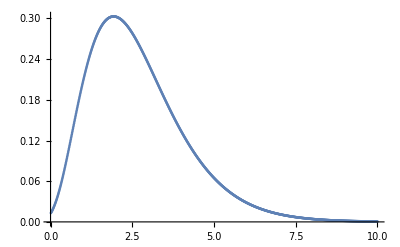

L:\Kut2\MM\hist_jsq5_B5.csv

```mathematica
Ht=ILT[Hsfun,Table[t,{t,1/100,10,1/100}],60,"cme",200];
Htlist = Table[{i/100,Ht[[i]]/norm},{i,1,1000}];
ListPlot[Htlist]
Export["L:\\Kut2\\MM\\hist_jsq5_B5.csv",N[Htlist,6],"Table","FieldSeparator"->","]
```

```mathematica
(* JBT system time distribution solver *)
(* FIFO service, homogeneous system *)
B=5;
(* threshold *)
M=4;
λ=5/4;
μ={1,11/10,12/10,13/10,14/10};
{ν[0],ν[1],ν[2],ν[3],ν[4],ν[5]}={005283,020330,071123,228085,675179,0}/1000000;
(* ratio of available servers *)
y=ν[0]+ν[1]+ν[2]+ν[3];
eqns={};
For[j=1,j≤M,j++,
For[i=1,i≤j,i++,
eqn={};
If[(i>1&&j<M),
eqn={Hs[i,j]==
(λ/y+μ[[j]])/(s+λ/y+μ[[j]])*
((λ/y)/(λ/y+μ[[j]])Hs[i,j+1]+μ[[j]]/(λ/y+μ[[j]])Hs[i-1,j-1])}];
If[(i>1)&&(j==M),
eqn={Hs[i,M]==
μ[[M]]/(s+μ[[M]])*Hs[i-1,M-1]}];
If[(i==1)&&(j≤M-1),
eqn={Hs[1,j]==(λ/y+μ[[j]])/(s+λ/y+μ[[j]])*((λ/y)/(λ/y+μ[[j]])*Hs[i,j+1]+
μ[[j]]/(λ/y+μ[[j]]))}];
If[(i==1)&&(j==M),
eqn={Hs[1,M]==
μ[[M]]/(s+μ[[M]])}];
eqns = eqns ~Join~eqn;
];
];
```

```mathematica
{Hs1,Hs2,Hs3,Hs4}={Hs[1,1],Hs[2,2],Hs[3,3],Hs[4,4]}/.Solve[eqns][[1]];
Hssol=ν[0]/y*Hs1+ν[1]/y*Hs2+ν[2]/y*Hs3+ν[3]/y*Hs4;
Hsfun[s_]:=Evaluate[Hssol];
```

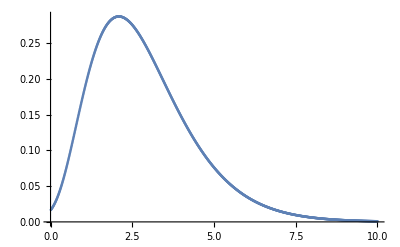

L:\Kut2\MM\hist_jbt.csv

```mathematica
Ht=ILT[Hsfun,Table[t,{t,1/100,10,1/100}],60,"cme",100];
Htlist = Table[{i/100,Ht[[i]]},{i,1,1000}];
ListPlot[Htlist]
Export["L:\\Kut2\\MM\\hist_jbt_B5.csv",N[Htlist,6],"Table","FieldSeparator"->","]
```